# Cuaderno de Prácticas

## Análisis y métodos numéricos

## Grado en Ingeniería Informática

## CURSO 2024/25

## Datos personales

Nombre y apellidos : Francisco Javier Martín - Lunas Escobar
DNI : 26268082
Grupo de teoría : 2
Grupo de prácticas :

## Práctica 14

### Mínimos cuadrados

Encontrar la recta que mejor aproxime en el sentido de los mínimos cuadrados a los datos (1,1,), (2,3), (4,7), (7,12), (8,15).

```mathematica
p[x_]:= a+b*x
error[a_,b_]:=(p[1]-1)^2 +(p[2]-3)^2 +(p[4]-7)^2 +(p[7]-12)^2 +(p[8]-15)^2
error[a,b]
```

(-1+a+b)^2+(-3+a+2 b)^2+(-7+a+4 b)^2+(-12+a+7 b)^2+(-15+a+8 b)^2

```mathematica
Solve[{D[error[a,b],a]==0,D[error[a,b],b]==0},{a,b}]
```

{{a→-83/93,b→359/186}}

```mathematica
p[x]/.%
```

{-83/93+(359 x)/186}

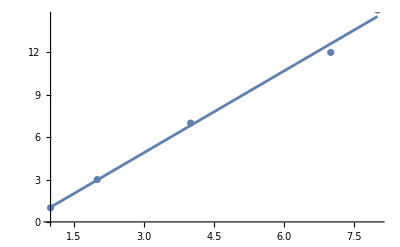

```mathematica
Show[Plot[-83/93+(359 x)/186,{x,1,8}],ListPlot[{{1,1},{2,3},{4,7},{7,12},{8,15}}]]
```

Calcular la parábola que mejor aproxima en el sentido de los mínimos cuadrados los datos (1,5),(2,4),(4,4),(7,12),(8,20),(10,30).

```mathematica
datos={{1,5},{2,4},{4,4},{7,12},{8,20},{10,30}};
n=Length[datos];
min=Min[Table[datos[[i]][[1]],{i,1,n}]];
max=Max[Table[datos[[i]][[1]],{i,1,n}]];
q[x_]:=a+b*x+c*x^2
er[a_,b_,c_]:=∑_(i=1)^n (q[datos[[i]][[1]]]-datos[[i]][[2]])^2 (* (q(xi)-yi)^2 *)
Solve[{D[er[a,b,c],a]==0,D[er[a,b,c],b]==0,D[er[a,b,c],c]==0},{a,b,c}]
```

{{a→12693/1810,b→-4719/1810,c→90/181}}